```mathematica
(*1. Построить график функции на отрезке от 0 до 1*)
```

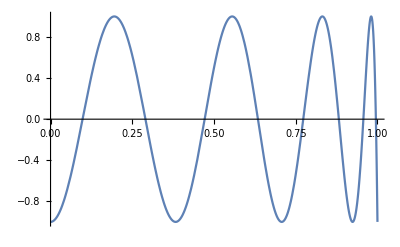

```mathematica
Plot[1-2*(1-2*(1-2*(1-2*x^2)^2)^2)^2, {x, 0 ,1}]
```

```mathematica
(*2. Построить график поверхности, число точек 40, названия осей X Y Z*)
```

```mathematica
Plot3D[Sin[x/(y+π/10)], {x, 0, 2*π}, {y, 0, π/2}, PlotPoints->40]
```

-Graphics3D-

```mathematica
(*3. Решить уравнения относительно переменной x*)
```

```mathematica
Solve[Log[x+Sqrt[x^2+a]] == b,x]
```

{{x→1/2 ⅇ^-b (-a+ⅇ^(2 b))}}

```mathematica
Solve[Log[Sqrt[x]] == Sqrt[Log[x]], x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1},{x→ⅇ^4}}

```mathematica
Solve[x^4-5*x^2-3 == 0, x]
```

{{x→-ⅈ √(1/2 (-5+√37))},{x→ⅈ √(1/2 (-5+√37))},{x→-√(1/2 (5+√37))},{x→√(1/2 (5+√37))}}

```mathematica
Solve[x^3-3*x-1== 0, x]
```

{{x→1/(1/2 (1+ⅈ √3))^(1/3)+(1/2 (1+ⅈ √3))^(1/3)},{x→-1/2 (1-ⅈ √3) (1/2 (1+ⅈ √3))^(1/3)-(1/2 (1+ⅈ √3))^(2/3)},{x→-(1-ⅈ √3)/(2^(2/3) (1+ⅈ √3)^(1/3))-(1+ⅈ √3)^(4/3)/(2 2^(1/3))}}

```mathematica
Solve[Cos[x]== Tan[x], x]
```

{{x→ConditionalExpression[π-ArcTan[√(1/2 (-1+√5))]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[√(1/2 (-1+√5))]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[-ⅈ √(1/2 (1+√5)),1/2 (-1-√5)]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[ⅈ √(1/2 (1+√5)),1/2 (-1-√5)]+2 π C[1],C[1]∈ℤ]}}

```mathematica
Reduce[a*x^4+b*x^3+1==0, x]
```

(a≠0&&(x==Root[1+b #1^3+a #1^4&,1]||x==Root[1+b #1^3+a #1^4&,2]||x==Root[1+b #1^3+a #1^4&,3]||x==Root[1+b #1^3+a #1^4&,4]))||(a==0&&b≠0&&(x==-1/b^(1/3)||x==(-1)^(1/3)/b^(1/3)||x==-(-1)^(2/3)/b^(1/3)))

```mathematica
(*4. Найти численное решение уравнения*)
```

```mathematica
NSolve[x^7+7*x==7,x]
```

{{x→-1.3217-0.706695 ⅈ},{x→-1.3217+0.706695 ⅈ},{x→-0.137797-1.43289 ⅈ},{x→-0.137797+1.43289 ⅈ},{x→0.920191},{x→0.999402-0.797172 ⅈ},{x→0.999402+0.797172 ⅈ}}

```mathematica
FindRoot[Cos[x] == x, {x, 1}]
```

{x→0.739085}

```mathematica
(*Начальное приближение для корня опеределить графически*)
```

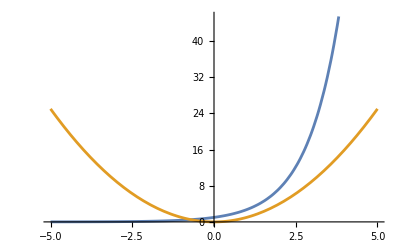

```mathematica
Plot[{Exp[x], x^2}, {x, -5,5}]
```

```mathematica
FindRoot[Exp[x] == x^2, {x, -2}]
```

{x→-0.703467}

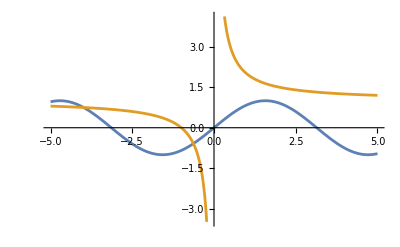

```mathematica
Plot[{Sin[x], 1+1/x}, {x, -5, 5}]
```

```mathematica
FindRoot[Sin[x] == 1+1/x, {x, -0.65}]
```

{x→-0.629446}

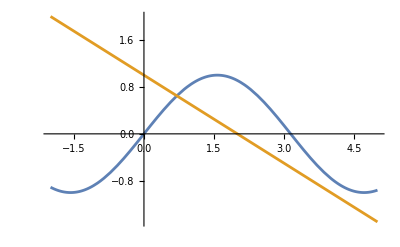

```mathematica
(*Для определения корней воспользуйтесь графиками функций, заданных в неявном виде*)
Plot[{Sin[x], 1-x/2}, {x, -2, 5}]
```

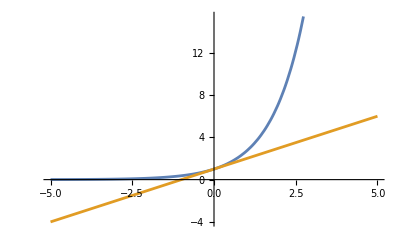

```mathematica
Plot[{E^x, x+1}, {x, -5, 5}]
```

```mathematica
(*5. Решить систему*)
```

```mathematica
sol = Solve[{x+y== 5, x-y ==1}, {x, y} ]
{x+y==5, x-y==1}/. sol
```

{{x→3,y→2}}

{{True,True}}

```mathematica
sol1 = Reduce[{Sqrt[x+y]== Sqrt[x*y], x^2+y^2 ==1}, {x, y} ]
{Sqrt[x+y]== Sqrt[x*y], x^2+y^2 ==1}/. sol1
```

(x==Root[-1+2 #1+#1^2-2 #1^3+#1^4&,1]&&y==-1+Root[-1+2 #1+#1^2-2 #1^3+#1^4&,1]^2-Root[-1+2 #1+#1^2-2 #1^3+#1^4&,1]^3)||(x==Root[-1+2 #1+#1^2-2 #1^3+#1^4&,2]&&y==-1+Root[-1+2 #1+#1^2-2 #1^3+#1^4&,2]^2-Root[-1+2 #1+#1^2-2 #1^3+#1^4&,2]^3)||(x==Root[-1+2 #1+#1^2-2 #1^3+#1^4&,3]&&y==-1+Root[-1+2 #1+#1^2-2 #1^3+#1^4&,3]^2-Root[-1+2 #1+#1^2-2 #1^3+#1^4&,3]^3)||(x==Root[-1+2 #1+#1^2-2 #1^3+#1^4&,4]&&y==-1+Root[-1+2 #1+#1^2-2 #1^3+#1^4&,4]^2-Root[-1+2 #1+#1^2-2 #1^3+#1^4&,4]^3)

ReplaceAll::reps: {(x==Root[-1+Times[«2»]+Power[«2»]+Times[«2»]+Power[«2»]&,1,0]&&y==-1+Root[«1»&,1,0]^2-Root[«3»]^3)||(x==Root[-1+Times[«2»]+Power[«2»]+Times[«2»]+Power[«2»]&,2,0]&&y==-1+Root[«1»&,2,0]^2-Root[«3»]^3)||(«1»)||(x==Root[-1+Times[«2»]+Power[«2»]+Times[«2»]+Power[«2»]&,4,0]&&y==-1+Root[«1»&,4,0]^2-Root[«3»]^3)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{√(x+y)==√(x y),x^2+y^2==1}/.(x==Root[-1+2 #1+#1^2-2 #1^3+#1^4&,1]&&y==-1+Root[-1+2 #1+#1^2-2 #1^3+#1^4&,1]^2-Root[-1+2 #1+#1^2-2 #1^3+#1^4&,1]^3)||(x==Root[-1+2 #1+#1^2-2 #1^3+#1^4&,2]&&y==-1+Root[-1+2 #1+#1^2-2 #1^3+#1^4&,2]^2-Root[-1+2 #1+#1^2-2 #1^3+#1^4&,2]^3)||(x==Root[-1+2 #1+#1^2-2 #1^3+#1^4&,3]&&y==-1+Root[-1+2 #1+#1^2-2 #1^3+#1^4&,3]^2-Root[-1+2 #1+#1^2-2 #1^3+#1^4&,3]^3)||(x==Root[-1+2 #1+#1^2-2 #1^3+#1^4&,4]&&y==-1+Root[-1+2 #1+#1^2-2 #1^3+#1^4&,4]^2-Root[-1+2 #1+#1^2-2 #1^3+#1^4&,4]^3)

```mathematica
sol1 = Reduce[{Sin[x+y]== Cos[x-y], Tan[x*y] ==Cos[x*y]}, {x, y} ]
{Sin[x+y]== Cos[x-y], Tan[x*y] ==Cos[x*y]}/. sol1
```

((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[1]≠0&&x==-2 ArcTan[1-√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,1]]+2 π C[2]))/(2 ArcTan[1-√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[1]≠0&&x==-2 ArcTan[1-√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,2]]+2 π C[2]))/(2 ArcTan[1-√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[1]≠0&&x==-2 ArcTan[1-√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,3]]+2 π C[2]))/(2 ArcTan[1-√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[1]≠0&&x==-2 ArcTan[1-√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,4]]+2 π C[2]))/(2 ArcTan[1-√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[1]≠0&&x==-2 ArcTan[1-√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,1]]+2 π C[2]))/(2 ArcTan[1-√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[1]≠0&&x==-2 ArcTan[1-√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,2]]+2 π C[2]))/(2 ArcTan[1-√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[1]≠0&&x==-2 ArcTan[1-√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,3]]+2 π C[2]))/(2 ArcTan[1-√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[1]≠0&&x==-2 ArcTan[1-√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,4]]+2 π C[2]))/(2 ArcTan[1-√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[1]≠0&&x==-2 ArcTan[1+√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,1]]+2 π C[2]))/(2 ArcTan[1+√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[1]≠0&&x==-2 ArcTan[1+√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,2]]+2 π C[2]))/(2 ArcTan[1+√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[1]≠0&&x==-2 ArcTan[1+√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,3]]+2 π C[2]))/(2 ArcTan[1+√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[1]≠0&&x==-2 ArcTan[1+√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,4]]+2 π C[2]))/(2 ArcTan[1+√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[1]≠0&&x==-2 ArcTan[1+√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,1]]+2 π C[2]))/(2 ArcTan[1+√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[1]≠0&&x==-2 ArcTan[1+√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,2]]+2 π C[2]))/(2 ArcTan[1+√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[1]≠0&&x==-2 ArcTan[1+√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,3]]+2 π C[2]))/(2 ArcTan[1+√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[1]≠0&&x==-2 ArcTan[1+√2]-2 π C[1]&&y==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,4]]+2 π C[2]))/(2 ArcTan[1+√2]+2 π C[1])))||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,1]]+2 π C[1]))/(2 ArcTan[1-√2]+2 π C[2]))&&y==-2 ArcTan[1-√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,2]]+2 π C[1]))/(2 ArcTan[1-√2]+2 π C[2]))&&y==-2 ArcTan[1-√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,3]]+2 π C[1]))/(2 ArcTan[1-√2]+2 π C[2]))&&y==-2 ArcTan[1-√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,4]]+2 π C[1]))/(2 ArcTan[1-√2]+2 π C[2]))&&y==-2 ArcTan[1-√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,1]]+2 π C[1]))/(2 ArcTan[1-√2]+2 π C[2]))&&y==-2 ArcTan[1-√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,2]]+2 π C[1]))/(2 ArcTan[1-√2]+2 π C[2]))&&y==-2 ArcTan[1-√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,3]]+2 π C[1]))/(2 ArcTan[1-√2]+2 π C[2]))&&y==-2 ArcTan[1-√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1-√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,4]]+2 π C[1]))/(2 ArcTan[1-√2]+2 π C[2]))&&y==-2 ArcTan[1-√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,1]]+2 π C[1]))/(2 ArcTan[1+√2]+2 π C[2]))&&y==-2 ArcTan[1+√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,2]]+2 π C[1]))/(2 ArcTan[1+√2]+2 π C[2]))&&y==-2 ArcTan[1+√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,3]]+2 π C[1]))/(2 ArcTan[1+√2]+2 π C[2]))&&y==-2 ArcTan[1+√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1+6 #1-2 #1^3+#1^4&,4]]+2 π C[1]))/(2 ArcTan[1+√2]+2 π C[2]))&&y==-2 ArcTan[1+√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,1]]+2 π C[1]))/(2 ArcTan[1+√2]+2 π C[2]))&&y==-2 ArcTan[1+√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,2]]+2 π C[1]))/(2 ArcTan[1+√2]+2 π C[2]))&&y==-2 ArcTan[1+√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,3]]+2 π C[1]))/(2 ArcTan[1+√2]+2 π C[2]))&&y==-2 ArcTan[1+√2]-2 π C[2])||((C[1]|C[2])∈ℤ&&ArcTan[1+√2]+π C[2]≠0&&x==-((2 (2 ArcTan[Root[-1-2 #1+6 #1^3+#1^4&,4]]+2 π C[1]))/(2 ArcTan[1+√2]+2 π C[2]))&&y==-2 ArcTan[1+√2]-2 π C[2])

```mathematica
(*6. Найти численно решение системы*)
```

```mathematica
Eliminate[{x^2+y^2-z^2==1,x+y==z,Sinh[z]-x^2==y^2}, {x, y}]
```

Sinh[z]==1+z^2

```mathematica
(*7. Решить дифференциальное уравнение*)
```

```mathematica
DSolve[y''[x]*x^2+5*y'[x]*x+y[x]==0, y, x]
```

{{y→Function[{x},x^(-2-√3) C[1]+x^(-2+√3) C[2]]}}

```mathematica
DSolve[y''[x]*x^2+3*y'[x]*x+y[x]==Sin[2*x], y, x]
```

{{y→Function[{x},C[1]/x-CosIntegral[2 x]/(2 x)+(C[2] Log[x])/x]}}

```mathematica
NDSolve[{y''[x]*x^2+5*y'[x]*x+y[x]==x^(-2+Sqrt[3]),y[1]==-1/12, y'[1]== 1/12*(2+Sqrt[3])}, y, x]
```

```mathematica
(*8. Решить систему аналитически*)
```

```mathematica
DSolve[y''[x]+y[x]/(Sin[x])^2==0, y[x], x]
```

{{y[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[-1/2,(ⅈ √3)/2,Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[-1/2,(ⅈ √3)/2,Cos[x]]}}

```mathematica
DSolve[{x'[t]==t^2+y[t], y'[t]==x[t]}, {y[t], x[t]}, t]
```

{{x[t]→1/4 ⅇ^(-2 t) (-1+ⅇ^(2 t)) (-2-2 t-t^2-ⅇ^(2 t) (2-2 t+t^2))+1/4 ⅇ^(-2 t) (1+ⅇ^(2 t)) (-2-2 t-t^2+ⅇ^(2 t) (2-2 t+t^2))+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2],y[t]→1/4 ⅇ^(-2 t) (1+ⅇ^(2 t)) (-2-2 t-t^2-ⅇ^(2 t) (2-2 t+t^2))+1/4 ⅇ^(-2 t) (-1+ⅇ^(2 t)) (-2-2 t-t^2+ⅇ^(2 t) (2-2 t+t^2))+1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]}}

```mathematica
DSolve[{y''[t]==4x[t]-5y[t], x''[t]==4y[t]-5x[t], y[0]==1, y'[0]==0, x[0]==0, x'[0]==1}, {y[t], x[t]}, t]
```

{{x[t]→1/6 (3 Cos[t]-3 Cos[3 t]+3 Sin[t]+Sin[3 t]),y[t]→1/6 (3 Cos[t]+3 Cos[3 t]+3 Sin[t]-Sin[3 t])}}

```mathematica
(*9. Решить уравнение, построить график решения*)
```

```mathematica
solution = DSolve[{x''[t]==-Sin[x[t]], x[0]==0, x'[0]==1.999}, x[t], t]
```

{{x[t]→2. JacobiAmplitude[0.9995 t,1.001]}}

```mathematica
f[x_]=x[t]/. solution[[1]]
```

2. JacobiAmplitude[0.9995 t,1.001]

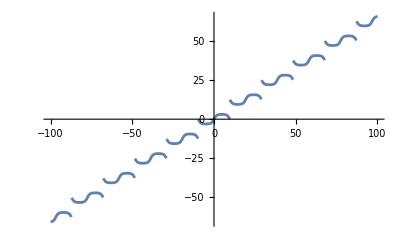

```mathematica
Plot[2.JacobiAmplitude[0.9995 t,1.0010007505003125], {t, -100, 100}]
```